## Masses

```mathematica
(* baryons *)
Nu=939.6(*0*);Δ=1232.0(*0*);Λ=1115.68(*0*);Σ=1192.6(*0*);Σs=1383.7(*0*);Ξ=1314.86(*0*);Ξs=1531.8(*0*);Ω=1672.45(*-*);Λc=2286.46(*+*);Σc=2453.75(*0*);Σcs=2518.48(*0*);Ξc=2470.44(*0*);Ξcp=2578.7(*0*);Ξcs=2646.16(*0*);
Λb=5619.6(*0*);
Σb=5813.1(*+-*);
Σbs=5832.53(*+-*);Ξb=5791.9(*0*);Ξbp=5935.0(*-*);Ξbs=5955.33(*-*);Ξcc=3621.6(*++*);Ξccs=3728.1(*Karliner*);Ξbb=10091.0(*Lattice*);Ξbbs=10103.0(*Lattice*);Ξbc=6943.0(*Lattice*);Ξbcs=6985.0(*Lattice*);Ωc=2695.2(*0*);Ωcs=2765.9(*0*);Ωb=6045.2(*-*);

(* mesons *)
πm=154.0(*Ebert*);ρm=775.26(*0*);Km=497.6(*0*);Kms=895.55(*0*);η=547.86(*0*);ηp=957.78(*0*);ϕ=1019.46(*0*);Dm=1864.84(*0*);Dms=2006.85(*0*);Bm=5279.66(*0*);Bms=5324.71(*0*);Dsm=1968.35(*+-*);Dsms=2112.2(*+-*);Bsm=5366.92(*0*);Bsms=5415.4(*0*);ηc=2983.9(*0*);ηb=9398.7(*0*);Jψ=3096.9(*0*);Υ=9460.3(*0*);Bcm=6274.47(*+*);Bcms=6332.0(*Ebert*);

(* reduced masses *)
mn=230;
ms=328;
mc=1440;
mb=4480;
μbb=N[mb*mb/(mb+mb)];
μbc=N[mb*mc/(mb+mc)];
μcc=N[mc*mc/(mc+mc)];
μbs=N[mb*ms/(mb+ms)];
μcs=N[mc*ms/(mc+ms)];
μbn=N[mb*mn/(mb+mn)];
μcn=N[mc*mn/(mc+mn)];
μss=N[ms*ms/(ms+ms)];
μsn=N[ms*mn/(ms+mn)];
μnn=N[mn*mn/(mn+mn)];

Print[{"μnn="<>ToString[μnn],"μsn="<>ToString[μsn],"μss="<>ToString[μss],"μcn="<>ToString[μcn],"μcs="<>ToString[μcs],"μcc="<>ToString[μcc],"μbn="<>ToString[μbn],"μbs="<>ToString[μbs],"μbc="<>ToString[μbc],"μbb="<>ToString[μbb]}];

(* isospin splittings *)
πuudd=135;πud=139.57;ρuudd=775.26;ρud=775.11;
Kmu=493.68;Kmd=497.61;Kmsu=891.67;Kmsd=895.55;
Dmu=1864.84;Dmd=1869.66;Dmsu=2006.85;Dmsd=2010.26;
Bmu=5279.34;Bmd=5279.66;Bmsn=5324.71;
p=938.27;n=939.57;
Λud=1115.68;Σuu=1189.37;Σud=1192.64;Σdd=1197.45;Σsuu=1382.8;Σsud=1383.7;Σsdd=1387.2;
Ξu=1314.86;Ξd=1321.71;Ξsu=1531.8;Ξsd=1535;
Λcud=2286.46;Σcuu=2453.97;Σcud=2452.65;Σcdd=2453.75;Σcsuu=2518.41;Σcsud=2517.4;Σcsdd=2518.48;
Λbud=5619.6;Σbuu=5810.56;Σbdd=5815.64;Σbsuu=5830.32;Σbsdd=5834.74;
Ξcu=2467.71;Ξcd=2470.44;Ξcpu=2578.2;Ξcpd=2578.7;Ξcsu=2645.1;Ξcsd=2646.16;
Ξbu=5791.9;Ξbd=5797;Ξbpd=5935.02;Ξbsu=5952.3;Ξbsd=5955.33;

(* assumed pseudoscalar ssbar meson *)
pseudoϕ[x_]:=(Kmu^2+Kmd^2-πuudd^2)^(1/2)/;x==1
pseudoϕ[x_]:=2η/3+ηp/3/;x==2
pseudoϕ[x_]:=ϕ-(Kms-Km)mn/ms/;x==3
pseudoϕ[x_]:=ϕ-(ρm-πm)mn^2/ms^2/;x==4
pseudoϕ[x_]:=743(*Ebert*)/;x==5
ϕ0=pseudoϕ[5]
```

{μnn=115.,μsn=135.197,μss=164.,μcn=198.323,μcs=267.149,μcc=720.,μbn=218.769,μbs=305.624,μbc=1089.73,μbb=2240.}

743

## Mass Splittings

{Annbar=1.54053×10^6,Asnbar=1.4073×10^6,Assbar=1.39419×10^6,Acnbar=2.19376×10^6,Acsbar=3.18484×10^6,Accbar=1.09836×10^7,Abnbar=2.18364×10^6,Absbar=3.3393×10^6,Abcbar=1.73971×10^7,Abbbar=5.79533×10^7}

{Ann=1.02702×10^6,Asn=938202.,Ass=929459.,Acn=1.46251×10^6,Acs=2.12323×10^6,Acc=7.3224×10^6,Abn=1.45576×10^6,Abs=2.2262×10^6,Abc=1.1598×10^7,Abb=3.86355×10^7}

0.0080881 μ+0.00794236 μ^2-0.0000684846 Log[μ^2]

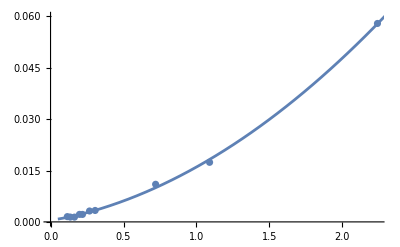

```mathematica
Annbar=mn*mn(ρm-πm)/(16/3+16);
Asnbar=ms*mn((Kmsu+Kmsd)/2-(Kmu+Kmd)/2)/(16/3+16);
Assbar=ms*ms(ϕ-ϕ0)/(16/3+16);
Acnbar=mc*mn((Dmsu+Dmsd)/2-(Dmu+Dmd)/2)/(16/3+16);
Acsbar=mc*ms(Dsms-Dsm)/(16/3+16);
Accbar=mc*mc(Jψ-ηc)/(16/3+16);
Abnbar=mb*mn(Bmsn-(Bmu+Bmd)/2)/(16/3+16);
Absbar=mb*ms(Bsms-Bsm)/(16/3+16);
Abcbar=mb*mc(Bcms-Bcm)/(16/3+16);
Abbbar=mb*mb(Υ-ηb)/(16/3+16);

Ann=2Annbar/3;
Asn=2Asnbar/3;
Ass=2Assbar/3;
Acn=2Acnbar/3;
Acs=2Acsbar/3;
Acc=2Accbar/3;
Abn=2Abnbar/3;
Absq=2Absbar/3;
Abc=2Abcbar/3;
Abb=2Abbbar/3;

Print[{"Annbar="<>ToString[Annbar,FormatType->TraditionalForm],"Asnbar="<>ToString[Asnbar,FormatType->TraditionalForm],"Assbar="<>ToString[Assbar,FormatType->TraditionalForm],"Acnbar="<>ToString[Acnbar,FormatType->TraditionalForm],"Acsbar="<>ToString[Acsbar,FormatType->TraditionalForm],"Accbar="<>ToString[Accbar,FormatType->TraditionalForm],"Abnbar="<>ToString[Abnbar,FormatType->TraditionalForm],"Absbar="<>ToString[Absbar,FormatType->TraditionalForm],"Abcbar="<>ToString[Abcbar,FormatType->TraditionalForm],"Abbbar="<>ToString[Abbbar,FormatType->TraditionalForm]}];
Print[{"Ann="<>ToString[Ann,FormatType->TraditionalForm],"Asn="<>ToString[Asn,FormatType->TraditionalForm],"Ass="<>ToString[Ass,FormatType->TraditionalForm],"Acn="<>ToString[Acn,FormatType->TraditionalForm],"Acs="<>ToString[Acs,FormatType->TraditionalForm],"Acc="<>ToString[Acc,FormatType->TraditionalForm],"Abn="<>ToString[Abn,FormatType->TraditionalForm],"Abs="<>ToString[Absq,FormatType->TraditionalForm],"Abc="<>ToString[Abc,FormatType->TraditionalForm],"Abb="<>ToString[Abb,FormatType->TraditionalForm]}];

dataA1={{μnn*10^(-3),Annbar*10^(-9)},{μsn*10^(-3),Asnbar*10^(-9)},{μss*10^(-3),Assbar*10^(-9)},{μcn*10^(-3),Acnbar*10^(-9)},{μcs*10^(-3),Acsbar*10^(-9)},{μcc*10^(-3),Accbar*10^(-9)},{μbn*10^(-3),Abnbar*10^(-9)},{μbs*10^(-3),Absbar*10^(-9)},{μbc*10^(-3),Abcbar*10^(-9)},{μbb*10^(-3),Abbbar*10^(-9)}};
fitA1=Fit[dataA1,{μ,μ^2,Log[μ^2]},μ]
Show[ListPlot[dataA1,PlotRange->{0,0.06}],Plot[fitA1,{μ,0.05,3.0}]]
```

```mathematica
{"snbar ssbar nnbar"}
ΔCsn0=-16 Asnbar/(ms*mn)-(-16 Assbar/(ms*ms)-16 Annbar/(mn*mn))/2;
Print["ΔK-(Δϕ0+Δπ)/2="<> ToString[ΔCsn0]];
ΔCsn1=16/3 Asnbar/(ms*mn)-(16/3 Assbar/(ms*ms)+16/3 Annbar/(mn*mn))/2;
Print["ΔK^*-(Δϕ+Δρ)/2="<> ToString[ΔCsn1]];

{"cnbar ccbar nnbar"}
ΔCcn0=-16 Acnbar/(mc*mn)-(-16 Accbar/(mc*mc)-16 Annbar/(mn*mn))/2;
Print["ΔD-(Δηc+Δπ)/2="<> ToString[ΔCcn0]];
ΔCcn1=16/3 Acnbar/(mc*mn)-(16/3 Accbar/(mc*mc)+16/3 Annbar/(mn*mn))/2;
Print["ΔD^*-(ΔJψ+Δρ)/2="<> ToString[ΔCcn1]];

{"bnbar bbbar nnbar"}
ΔCbn0=-16 Abnbar/(mb*mn)-(-16 Abbbar/(mb*mb)-16 Annbar/(mn*mn))/2;
Print["ΔB-(Δηb+Δπ)/2="<> ToString[ΔCbn0]];
ΔCbn1=16/3 Abnbar/(mb*mn)-(16/3 Abbbar/(mb*mb)+16/3 Annbar/(mn*mn))/2;
Print["ΔB^*-(ΔΥ+Δρ)/2="<> ToString[ΔCbn1]];

{"csbar ccbar ssbar"}
ΔCcs0=-16 Acsbar/(mc*ms)-(-16 Accbar/(mc*mc)-16 Assbar/(ms*ms))/2;
Print["ΔDs-(Δηc+Δϕ0)/2="<> ToString[ΔCcs0]];
ΔCcs1=16/3 Acsbar/(mc*ms)-(16/3 Accbar/(mc*mc)+16/3 Assbar/(ms*ms))/2;
Print["ΔDs^*-(ΔJψ+Δϕ)/2="<> ToString[ΔCcs1]];

{"bsbar bbbar ssbar"}
ΔCbs0=-16 Absbar/(mb*ms)-(-16 Abbbar/(mb*mb)-16 Assbar/(ms*ms))/2;
Print["ΔBs-(Δηb+Δϕ0)/2="<> ToString[ΔCbs0]];
ΔCbs1=16/3 Absbar/(mb*ms)-(16/3 Abbbar/(mb*mb)+16/3 Assbar/(ms*ms))/2;
Print["ΔBs^*-(ΔΥ+Δϕ)/2="<> ToString[ΔCbs1]];

{"bcbar bbbar ccbar"}
ΔCbc0=-16 Abcbar/(mb*mc)-(-16 Abbbar/(mb*mb)-16 Accbar/(mc*mc))/2;
Print["ΔBc-(Δηb+Δηc)/2="<> ToString[ΔCbc0]];
ΔCbc1=16/3 Abcbar/(mb*mc)-(16/3 Abbbar/(mb*mb)+16/3 Accbar/(mc*mc))/2;
Print["ΔBc^*-(ΔΥ+ΔJψ)/2="<> ToString[ΔCbc1]];

{"csn css cnn"}
ΔCcsn1=8/3 Asn/(ms*mn)-16/3 Acn/(mc*mn)-16/3 Acs/(mc*ms)-(8/3 Ass/(ms*ms)-32/3 Acs/(mc*ms)+8/3 Ann/(mn*mn)-32/3 Acn/(mc*mn))/2;
Print["ΔΞc'-(ΔΩc+ΔΣc)/2="<> ToString[ΔCcsn1]];
ΔCcsn3=8/3 Acs/(mc*ms)+8/3 Acn/(mc*mn)+8/3 Asn/(ms*mn)-(16/3 Acs/(mc*ms)+8/3 Ass/(ms*ms)+16/3 Acn/(mc*mn)+8/3 Ann/(mn*mn))/2;
Print["ΔΞc^*-(ΔΩc^*+ΔΣc^*)/2="<> ToString[ΔCcsn3]];

{"bsn bss bnn"}
ΔCbsn1=8/3 Asn/(ms*mn)-16/3 Abn/(mb*mn)-16/3 Absq/(mb*ms)-(8/3 Ass/(ms*ms)-32/3 Absq/(mb*ms)+8/3 Ann/(mn*mn)-32/3 Abn/(mb*mn))/2;
Print["ΔΞb'-(ΔΩb+ΔΣb)/2="<> ToString[ΔCbsn1]];
ΔCbsn3=8/3 Absq/(mb*ms)+8/3 Abn/(mb*mn)+8/3 Asn/(ms*mn)-(16/3 Absq/(mb*ms)+8/3 Ass/(ms*ms)+16/3 Abn/(mb*mn)+8/3 Ann/(mn*mn))/2;
Print["ΔΞb^*-(ΔΩb^*+ΔΣb^*)/2="<> ToString[ΔCbsn3]];

{"nsc nss ncc"}
ΔCnsc1=8/3 Asn/(ms*mn)-16/3 Acn/(mc*mn)-16/3 Acs/(mc*ms)-(8/3 Ass/(ms*ms)-32/3 Asn/(ms*mn)+8/3 Acc/(mc*mc)-32/3 Acn/(mc*mn))/2;
Print["ΔΞc'-(ΔΞ+ΔΞcc)/2="<> ToString[ΔCnsc1]];
ΔCnsc3=8/3 Asn/(ms*mn)+8/3 Acn/(mc*mn)+8/3 Acs/(mc*ms)-(16/3 Asn/(ms*mn)+8/3 Ass/(ms*ms)+16/3 Acn/(mc*mn)+8/3 Acc/(mc*mc))/2;
Print["ΔΞc^*-(ΔΞ^*+ΔΞcc^*)/2="<> ToString[ΔCnsc3]];

{"nsb nss nbb"}
ΔCnsb1=8/3 Asn/(ms*mn)-16/3 Abn/(mb*mn)-16/3 Absq/(mb*ms)-(8/3 Ass/(ms*ms)-32/3 Asn/(ms*mn)+8/3 Abb/(mb*mb)-32/3 Abn/(mb*mn))/2;
Print["ΔΞb'-(ΔΞ+ΔΞbb)/2="<> ToString[ΔCnsb1]];
ΔCnsb3=8/3 Asn/(ms*mn)+8/3 Abn/(mb*mn)+8/3 Absq/(mb*ms)-(16/3 Asn/(ms*mn)+8/3 Ass/(ms*ms)+16/3 Abn/(mb*mn)+8/3 Abb/(mb*mb))/2;
Print["ΔΞb^*-(ΔΞ^*+ΔΞbb^*)/2="<> ToString[ΔCnsb3]];

{"ssn sss snn"}
ΔCssn3=8/3 Ass/(ms*ms)+16/3 Asn/(ms*mn)-(8 Ass/(ms*ms)+16/3 Asn/(ms*mn)+8/3 Ann/(mn*mn))/2;
Print["ΔΞ^*-(ΔΩ+ΔΣ^*)/2="<> ToString[ΔCssn3]];

{"ssc sss scc"}
ΔCssc3=8/3 Ass/(ms*ms)+16/3 Acs/(mc*ms)-(8 Ass/(ms*ms)+16/3 Acs/(mc*ms)+8/3 Acc/(mc*mc))/2;
Print["ΔΩc^*-(ΔΩ+ΔΩcc^*)/2="<> ToString[ΔCssc3]];

{"ssb sss sbb"}
ΔCssb3=8/3 Ass/(ms*ms)+16/3 Absq/(mc*ms)-(8 Ass/(ms*ms)+16/3 Absq/(mb*ms)+8/3 Abb/(mb*mb))/2;
Print["ΔΩb^*-(ΔΩ+ΔΩbb^*)/2="<> ToString[ΔCssb3]];

{"ccn ccc cnn"}
ΔCccn3=8/3 Acc/(mc*mc)+16/3 Acn/(mc*mn)-(8 Acc/(mc*mc)+16/3 Acn/(mc*mn)+8/3 Ann/(mn*mn))/2;
Print["ΔΞcc^*-(ΔΩccc+ΔΣc^*)/2="<> ToString[ΔCccn3]];

{"ccs ccc css"}
ΔCccs3=8/3 Acc/(mc*mc)+16/3 Acs/(mc*ms)-(8 Acc/(mc*mc)+16/3 Acs/(mc*ms)+8/3 Ass/(ms*ms))/2;
Print["ΔΩcc^*-(ΔΩccc+ΔΩc^*)/2="<> ToString[ΔCccs3]];

{"ccb ccc cbb"}
ΔCccb3=8/3 Acc/(mc*mc)+16/3 Abc/(mb*mc)-(8 Acc/(mc*mc)+16/3 Abc/(mb*mc)+8/3 Abb/(mb*mb))/2;
Print["ΔΩccb^*-(ΔΩccc+ΔΩcbb^*)/2="<> ToString[ΔCccb3]];

{"bbn bbb bnn"}
ΔCbbn3=8/3 Abb/(mb*mb)+16/3 Abn/(mb*mn)-(8 Abb/(mb*mb)+16/3 Abn/(mb*mn)+8/3 Ann/(mn*mn))/2;
Print["ΔΞbb^*-(ΔΩbbb+ΔΣb^*)/2="<> ToString[ΔCbbn3]];

{"bbs bbb bss"}
ΔCbbs3=8/3 Abb/(mb*mb)+16/3 Absq/(mb*ms)-(8 Abb/(mb*mb)+16/3 Absq/(mb*ms)+8/3 Ass/(ms*ms))/2;
Print["ΔΩbb^*-(ΔΩbbb+ΔΩb^*)/2="<> ToString[ΔCbbs3]];

{"bbc bbb bcc"}
ΔCbbc3=8/3 Abb/(mb*mb)+16/3 Abc/(mb*mc)-(8 Abb/(mb*mb)+16/3 Abc/(mb*mc)+8/3 Acc/(mc*mc))/2;
Print["ΔΩbbc^*-(ΔΩbbb+ΔΩbcc^*)/2="<> ToString[ΔCbbc3]];

{"bcn bcc bnn"}
ΔCbcn1=8/3 Abc/(mb*mc)-16/3 Abn/(mb*mn)-16/3 Acn/(mc*mn)-(8/3 Acc/(mc*mc)-32/3 Abc/(mb*mc)+8/3 Ann/(mn*mn)-32/3 Abn/(mb*mn))/2;
Print["ΔΞbc-(ΔΩbcc+ΔΣb)/2="<> ToString[ΔCbcn1]];
ΔCbcn3=8/3 Abc/(mb*mc)+8/3 Abn/(mb*mn)+8/3 Acn/(mc*mn)-(16/3 Abc/(mb*mc)+8/3 Acc/(mc*mc)+16/3 Abn/(mb*mn)+8/3 Ann/(mn*mn))/2;
Print["ΔΞbc^*-(ΔΩbcc^*+ΔΣb^*)/2="<> ToString[ΔCbcn3]];

{"bcs bcc bss"}
ΔCbcs1=8/3 Abc/(mb*mc)-16/3 Absq/(mb*ms)-16/3 Acs/(mc*ms)-(8/3 Acc/(mc*mc)-32/3 Abc/(mb*mc)+8/3 Ass/(ms*ms)-32/3 Absq/(mb*ms))/2;
Print["ΔΩbc-(ΔΩbcc+ΔΩb)/2="<> ToString[ΔCbcs1]];
ΔCbcs3=8/3 Abc/(mb*mc)+8/3 Absq/(mb*ms)+8/3 Acs/(mc*ms)-(16/3 Abc/(mb*mc)+8/3 Acc/(mc*mc)+16/3 Absq/(mb*ms)+8/3 Ass/(ms*ms))/2;
Print["ΔΩbc^*-(ΔΩbcc^*+ΔΩb^*)/2="<> ToString[ΔCbcs3]];
```

{snbar ssbar nnbar}

ΔK-(Δϕ0+Δπ)/2=38.1713

ΔK^*-(Δϕ+Δρ)/2=-12.7238

{cnbar ccbar nnbar}

ΔD-(Δηc+Δπ)/2=169.369

ΔD^*-(ΔJψ+Δρ)/2=-56.4563

{bnbar bbbar nnbar}

ΔB-(Δηb+Δπ)/2=222.165

ΔB^*-(ΔΥ+Δρ)/2=-74.055

{csbar ccbar ssbar}

ΔDs-(Δηc+Δϕ0)/2=38.16

ΔDs^*-(ΔJψ+Δϕ)/2=-12.72

{bsbar bbbar ssbar}

ΔBs-(Δηb+Δϕ0)/2=90.4125

ΔBs^*-(ΔΥ+Δϕ)/2=-30.1375

{bcbar bbbar ccbar}

ΔBc-(Δηb+Δηc)/2=22.3275

ΔBc^*-(ΔΥ+ΔJψ)/2=-7.4425

{csn css cnn}

ΔΞc'-(ΔΩc+ΔΣc)/2=-4.24125

ΔΞc^*-(ΔΩc^*+ΔΣc^*)/2=-4.24125

{bsn bss bnn}

ΔΞb'-(ΔΩb+ΔΣb)/2=-4.24125

ΔΞb^*-(ΔΩb^*+ΔΣb^*)/2=-4.24125

{nsc nss ncc}

ΔΞc'-(ΔΞ+ΔΞcc)/2=59.2888

ΔΞc^*-(ΔΞ^*+ΔΞcc^*)/2=-4.24

{nsb nss nbb}

ΔΞb'-(ΔΞ+ΔΞbb)/2=77.3254

ΔΞb^*-(ΔΞ^*+ΔΞbb^*)/2=-10.0458

{ssn sss snn}

ΔΞ^*-(ΔΩ+ΔΣ^*)/2=-4.24125

{ssc sss scc}

ΔΩc^*-(ΔΩ+ΔΩcc^*)/2=-4.24

{ssb sss sbb}

ΔΩb^*-(ΔΩ+ΔΩbb^*)/2=7.01194

{ccn ccc cnn}

ΔΞcc^*-(ΔΩccc+ΔΣc^*)/2=-18.8188

{ccs ccc css}

ΔΩcc^*-(ΔΩccc+ΔΩc^*)/2=-4.24

{ccb ccc cbb}

ΔΩccb^*-(ΔΩccc+ΔΩcbb^*)/2=-2.48083

{bbn bbb bnn}

ΔΞbb^*-(ΔΩbbb+ΔΣb^*)/2=-24.685

{bbs bbb bss}

ΔΩbb^*-(ΔΩbbb+ΔΩb^*)/2=-10.0458

{bbc bbb bcc}

ΔΩbbc^*-(ΔΩbbb+ΔΩbcc^*)/2=-2.48083

{bcn bcc bnn}

ΔΞbc-(ΔΩbcc+ΔΣb)/2=-39.7625

ΔΞbc^*-(ΔΩbcc^*+ΔΣb^*)/2=-18.8188

{bcs bcc bss}

ΔΩbc-(ΔΩbcc+ΔΩb)/2=-25.82

ΔΩbc^*-(ΔΩbcc^*+ΔΩb^*)/2=-4.24

## Mass Inequalities

```mathematica
{"snbar ssbar nnbar"}
ΔMsu0=Kmu-(ϕ0+πm)/2;ΔMsd0=Kmd-(ϕ0+πm)/2;ΔMsn0=(ΔMsu0+ΔMsd0)/2;
Print["K-(ϕ0+π)/2="<> ToString[ΔMsn0]];
ΔMsu1=Kmsu-(ϕ+ρm)/2;ΔMsd1=Kmsd-(ϕ+ρm)/2;ΔMsn1=(ΔMsu1+ΔMsd1)/2;
Print["K^*-(ϕ+ρ)/2="<> ToString[ΔMsn1]];
ΔMBsn=(ΔMsn0+3*ΔMsn1)/4;
Print["snbar-(ssbar+nnbar)/2="<> ToString[ΔMBsn]];

{"cnbar ccbar nnbar"}
ΔMcu0=Dmu-(ηc+πm)/2;ΔMcd0=Dmd-(ηc+πm)/2;ΔMcn0=(ΔMcu0+ΔMcd0)/2;
Print["D-(ηc+π)/2="<> ToString[ΔMcn0]];
ΔMcu1=Dmsu-(Jψ+ρm)/2;ΔMcd1=Dmsd-(Jψ+ρm)/2;ΔMcn1=(ΔMcu1+ΔMcd1)/2;
Print["D^*-(Jψ+ρ)/2="<> ToString[ΔMcn1]];
ΔMBcn=(ΔMcn0+3*ΔMcn1)/4;
Print["cnbar-(ccbar+nnbar)/2="<> ToString[ΔMBcn]];

{"bnbar bbbar nnbar"}
ΔMbu0=Bmu-(ηb+πm)/2;ΔMbd0=Bmd-(ηb+πm)/2;ΔMbn0=(ΔMbu0+ΔMbd0)/2;
Print["B-(ηb+π)/2="<> ToString[ΔMbn0]];
ΔMbn1=Bmsn-(Υ+ρm)/2;
Print["B^*-(Υ+ρ)/2="<> ToString[ΔMbn1]];
ΔMBbn=(ΔMbn0+3*ΔMbn1)/4;
Print["bnbar-(bbbar+nnbar)/2="<> ToString[ΔMBbn]];

{"csbar ccbar ssbar"}
ΔMcs0=Dsm-(ηc+ϕ0)/2;
Print["Ds-(ηc+ϕ0)/2="<> ToString[ΔMcs0]];
ΔMcs1=Dsms-(Jψ+ϕ)/2;
Print["Ds^*-(Jψ+ϕ)/2="<> ToString[ΔMcs1]];
ΔMBcs=(ΔMcs0+3*ΔMcs1)/4;
Print["csbar-(ccbar+ssbar)/2="<> ToString[ΔMBcs]];

{"bsbar bbbar ssbar"}
ΔMbs0=Bsm-(ηb+ϕ0)/2;
Print["Bs-(ηb+ϕ0)/2="<> ToString[ΔMbs0]];
ΔMbs1=Bsms-(Υ+ϕ)/2;
Print["Bs^*-(Υ+ϕ)/2="<> ToString[ΔMbs1]];
ΔMBbs=(ΔMbs0+3*ΔMbs1)/4;
Print["bsbar-(bbbar+ssbar)/2="<> ToString[ΔMBbs]];

{"bcbar bbbar ccbar"}
ΔMbc0=Bcm-(ηb+ηc)/2;
Print["Bc-(ηb+ηc)/2="<> ToString[ΔMbc0]];
ΔMbc1=Bcms-(Υ+Jψ)/2;
Print["Bc^*-(Υ+Jψ)/2="<> ToString[ΔMbc1]];
ΔMBbc=(ΔMbc0+3*ΔMbc1)/4;
Print["bcbar-(bbbar+ccbar)/2="<> ToString[ΔMBbc]];

{"usu uss uuu"}
ΔMusu3=Σsuu-(Ξsu+Δ)/2;
Print["Σuu^*-(Ξu^*+Δ)/2="<> ToString[ΔMusu3]];

{"usd uss udd"}
ΔMusd1=(Λud+Σud)/2-(Ξu+n+52)/2;
Print["(Λud+Σud)/2-(Ξu+n+52)/2="<> ToString[ΔMusd1]];

{"sud suu sdd"}
ΔMsud1=Σud-(Σuu+Σdd)/2;
Print["Σud-(Σuu+Σdd)/2="<> ToString[ΔMsud1]];
ΔMsud3=Σsud-(Σsuu+Σsdd)/2;
Print["Σud^*-(Σuu^*+Σdd^*)/2="<> ToString[ΔMsud3]];

{"ssn sss snn"}
ΔMssu3=Ξsu-(Ω+Σsuu)/2;ΔMssd3=Ξsd-(Ω+Σsdd)/2;ΔMssn3=(ΔMssu3+ΔMssd3)/2;
Print["Ξ^*-(Ω+Σ^*)/2="<> ToString[ΔMssn3]];

{"cud cuu cdd"}
ΔMcud1=Σcud-(Σcuu+Σcdd)/2;
Print["Σcud-(Σcuu+Σcdd)/2="<> ToString[ΔMcud1]];
ΔMcud3=Σcsud-(Σcsuu+Σcsdd)/2;
Print["Σcud^*-(Σcuu^*+Σcdd^*)/2="<> ToString[Σcsud-(Σcsuu+Σcsdd)/2]];

{"csn css cnn"}
ΔMcsu1=Ξcpu-(Ωc+Σcuu)/2;ΔMcsd1=Ξcpd-(Ωc+Σcdd)/2;ΔMcsn1=(ΔMcsu1+ΔMcsd1)/2;
Print["Ξc'-(Ωc+Σc)/2="<> ToString[ΔMcsn1]];
ΔMcsu3=Ξcsu-(Ωcs+Σcsuu)/2;ΔMcsd3=Ξcsd-(Ωcs+Σcsdd)/2;ΔMcsn3=(ΔMcsu3+ΔMcsd3)/2;
Print["Ξc^*-(Ωc^*+Σc^*)/2="<> ToString[ΔMcsn3]];
ΔMBcsn=(2*ΔMcsn1+4*ΔMcsn3)/6;
Print["csn-(css+cnn)/2="<> ToString[ΔMBcsn]];

{"nsc nss ncc"}
ΔMusc1=Ξcpu-(Ξu+Ξcc)/2;
Print["Ξc'-(Ξ+Ξcc)/2="<> ToString[ΔMusc1]];

{"bsn bss bnn"}
ΔMbsd1=Ξbpd-(Ωb+Σbdd)/2;ΔMbsn1=ΔMbsd1;
Print["Ξb'-(Ωb+Σb)/2="<> ToString[ΔMbsn1]];
```

{snbar ssbar nnbar}

K-(ϕ0+π)/2=47.145

K^*-(ϕ+ρ)/2=-3.75

snbar-(ssbar+nnbar)/2=8.97375

{cnbar ccbar nnbar}

D-(ηc+π)/2=298.3

D^*-(Jψ+ρ)/2=72.475

cnbar-(ccbar+nnbar)/2=128.931

{bnbar bbbar nnbar}

B-(ηb+π)/2=503.15

B^*-(Υ+ρ)/2=206.93

bnbar-(bbbar+nnbar)/2=280.985

{csbar ccbar ssbar}

Ds-(ηc+ϕ0)/2=104.9

Ds^*-(Jψ+ϕ)/2=54.02

csbar-(ccbar+ssbar)/2=66.74

{bsbar bbbar ssbar}

Bs-(ηb+ϕ0)/2=296.07

Bs^*-(Υ+ϕ)/2=175.52

bsbar-(bbbar+ssbar)/2=205.658

{bcbar bbbar ccbar}

Bc-(ηb+ηc)/2=83.17

Bc^*-(Υ+Jψ)/2=53.4

bcbar-(bbbar+ccbar)/2=60.8425

{usu uss uuu}

Σuu^*-(Ξu^*+Δ)/2=0.9

{usd uss udd}

(Λud+Σud)/2-(Ξu+n+52)/2=0.945

{sud suu sdd}

Σud-(Σuu+Σdd)/2=-0.77

Σud^*-(Σuu^*+Σdd^*)/2=-1.3

{ssn sss snn}

Ξ^*-(Ω+Σ^*)/2=4.675

{cud cuu cdd}

Σcud-(Σcuu+Σcdd)/2=-1.21

Σcud^*-(Σcuu^*+Σcdd^*)/2=-1.045

{csn css cnn}

Ξc'-(Ωc+Σc)/2=3.92

Ξc^*-(Ωc^*+Σc^*)/2=3.4575

csn-(css+cnn)/2=3.61167

{nsc nss ncc}

Ξc'-(Ξ+Ξcc)/2=109.97

{bsn bss bnn}

Ξb'-(Ωb+Σb)/2=4.6

## Bindings

```mathematica
(* spin-averaged masses *)
Mnnbar=(3ρm+πm)/4;Msnbar=(3Kms+Km)/4;Mssbar=(3ϕ+ϕ0)/4;Mcnbar=(3Dms+Dm)/4;Mcsbar=(3Dsms+Dsm)/4;Mccbar=(3Jψ+ηc)/4;Mbnbar=(3Bms+Bm)/4;Mbsbar=(3Bsms+Bsm)/4;Mbcbar=(3Bcms+Bcm)/4;Mbbbar=(3Υ+ηb)/4;

Mnnn=(4Δ+2Nu)/6;Msnn=(4Σs+2Σ)/6;Mssn=(4Ξs+2Ξ)/6;Mcnn=(4Σcs+2Σc)/6;Mcsn=(4Ξcs+2Ξcp)/6;Mccn=(4Ξccs+2Ξcc)/6;Mbnn=(4Σbs+2Σb)/6;Mbsn=(4Ξbs+2Ξbp)/6;Mbcn=(4Ξbcs+2Ξbc)/6;Mbbn=(4Ξbbs+2Ξbb)/6;

Bnnbar=0;
Bsnbar=0;
Bssbar=0(*Mssbar-2Msnbar+Mnnbar*);
Bcnbar=0;
Bbnbar=0;
Bcsbar=Mcsbar-Mcnbar-Msnbar+Mnnbar;Bbsbar=Mbsbar-Mbnbar-Msnbar+Mnnbar;Bccbar=Mccbar-2Mcnbar+Mnnbar;Bbcbar=Mbcbar-Mbnbar-Mcnbar+Mnnbar;Bbbbar=Mbbbar-2Mbnbar+Mnnbar;

Bnn=0;
Bsn=0;
Bss=0(*Mssn-2Msnn+Mnnn*);
Bcn=0;
Bbn=0;Bcs=Mcsn-Mcnn-Msnn+Mnnn;Bbs=Mbsn-Mbnn-Msnn+Mnnn;Bcc=Mccn-2Mcnn+Mnnn;Bbc=Mbcn-Mbnn-Mcnn+Mnnn;Bbb=Mbbn-2Mbnn+Mnnn;

Print[{"Mnnbar="<>ToString[Mnnbar],"Msnbar="<>ToString[Msnbar],"Mssbar="<>ToString[Mssbar],"Mcnbar="<>ToString[Mcnbar],"Mcsbar="<>ToString[Mcsbar],"Mccbar="<>ToString[Mccbar],"Mbnbar="<>ToString[Mbnbar],"Mbsbar="<>ToString[Mbsbar],"Mbcbar="<>ToString[Mbcbar],"Mbbbar="<>ToString[Mbbbar]}];
Print[{"Mnnn="<>ToString[Mnnn],"Msnn="<>ToString[Msnn],"Mssn="<>ToString[Mssn],"Mcnn="<>ToString[Mcnn],"Mcsn="<>ToString[Mcsn],"Mccn="<>ToString[Mccn],"Mbnn="<>ToString[Mbnn],"Mbsn="<>ToString[Mbsn],"Mbcn="<>ToString[Mbcn],"Mbbn="<>ToString[Mbbn]}];
Print[{"Bssbar="<>ToString[Bssbar],"Bcsbar="<>ToString[Bcsbar],"Bbsbar="<>ToString[Bbsbar],"Bccbar="<>ToString[Bccbar],"Bbcbar="<>ToString[Bbcbar],"Bbbbar="<>ToString[Bbbbar]}];
Print[{"Bss="<>ToString[Bss],"Bcs="<>ToString[Bcs],"Bbs="<>ToString[Bbs],"Bcc="<>ToString[Bcc],"Bbc="<>ToString[Bbc],"Bbb="<>ToString[Bbb]}];
```

{Mnnbar=619.945,Msnbar=796.062,Mssbar=950.345,Mcnbar=1971.35,Mcsbar=2076.24,Mccbar=3068.65,Mbnbar=5313.45,Mbsbar=5403.28,Mbcbar=6317.62,Mbbbar=9444.9}

{Mnnn=1134.53,Msnn=1320.,Mssn=1459.49,Mcnn=2496.9,Mcsn=2623.67,Mccn=3692.6,Mbnn=5826.05,Mbsn=5948.55,Mbcn=6971.,Mbbn=10099.}

{Bssbar=0,Bcsbar=-71.2275,Bbsbar=-86.285,Bccbar=-254.1,Bbcbar=-347.232,Bbbbar=-562.05}

{Bss=0,Bcs=-58.6967,Bbs=-62.9667,Bcc=-166.673,Bbc=-217.423,Bbb=-418.573}

## Binding Fittings

-127.774 μ^(1/3)+(218.413 μ^(1/3))/Log[μ^(1/3)]

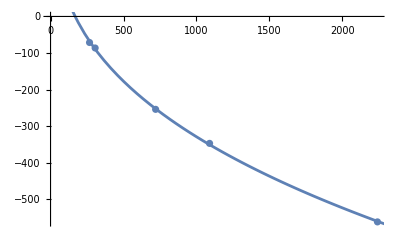

-92.643 μ^(1/3)+(159.994 μ^(1/3))/Log[μ^(1/3)]

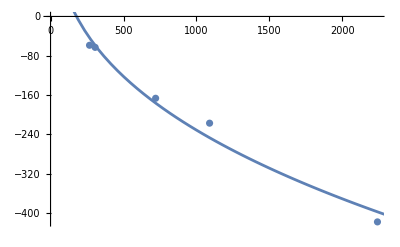

2/3 (-127.774 μ^(1/3)+(218.413 μ^(1/3))/Log[μ^(1/3)])

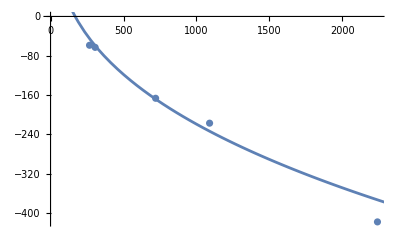

```mathematica
dataB1={{μbb,Bbbbar},{μbc,Bbcbar},{μcc,Bccbar},{μbs,Bbsbar},{μcs,Bcsbar}};
dataB2={{μbb,Bbb},{μbc,Bbc},{μcc,Bcc},{μbs,Bbs},{μcs,Bcs}};
ΛQ=200;
fitB1=Fit[dataB1,{(μ)^(1/3)/Log[μ^(1/3)],(μ)^(1/3)},μ]
Show[ListPlot[dataB1],Plot[fitB1,{μ,100,2300}]]
fitB2=Fit[dataB2,{(μ)^(1/3)/Log[μ^(1/3)],(μ)^(1/3)},μ]
Show[ListPlot[dataB2],Plot[fitB2,{μ,100,2300}]]
fitB1*2/3
Show[ListPlot[dataB2],Plot[fitB1*2/3,{μ,100,2300}]]
```

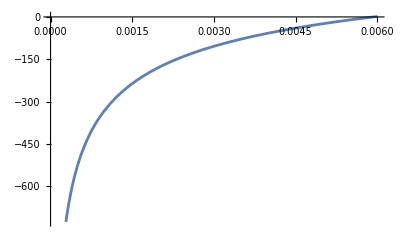

```mathematica
BD[r_]:=-127.77404505617989 (1/r)^(1/3)+(218.41303451372744 (1/r)^(1/3))/Log[(1/r)^(1/3)]
Plot[BD[R],{R,0,0.006}]
```

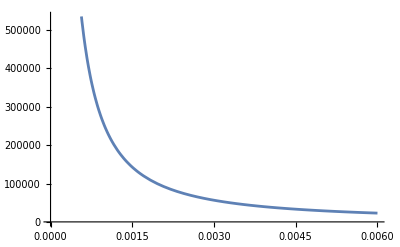

```mathematica
DBD[r_]=D[BD[R],R];
Plot[DBD[R],{R,0,0.006}]
```

```mathematica
Print[{"Bss="<>ToString[Bss],"Bcs="<>ToString[Bcs],"Bbs="<>ToString[Bbs],"Bcc="<>ToString[Bcc],"Bbc="<>ToString[Bbc],"Bbb="<>ToString[Bbb]}];

Bcs=2Bcsbar/3;
Bbs=2Bbsbar/3;
Bcc=2Bccbar/3;
Bbc=2Bbcbar/3;
Bbb=2Bbbbar/3;

Print[{"Bss="<>ToString[Bss],"Bcs="<>ToString[Bcs],"Bbs="<>ToString[Bbs],"Bcc="<>ToString[Bcc],"Bbc="<>ToString[Bbc],"Bbb="<>ToString[Bbb]}];
```

{Bss=0,Bcs=-58.6967,Bbs=-62.9667,Bcc=-166.673,Bbc=-217.423,Bbb=-418.573}

{Bss=0,Bcs=-47.485,Bbs=-57.5233,Bcc=-169.4,Bbc=-231.488,Bbb=-374.7}

## Binding Inequalities

```mathematica
(* mesons *)
ΔBsn=Bsnbar-(Bssbar+Bnnbar)/2;Print["Bsnbar-(Bnnbar+Bssbar)/2="<> ToString[ΔBsn]];
ΔBcn=Bcnbar-(Bccbar+Bnnbar)/2;Print["Bcnbar-(Bnnbar+Bccbar)/2="<> ToString[ΔBcn]];
ΔBbn=Bbnbar-(Bbbbar+Bnnbar)/2;Print["Bbnbar-(Bnnbar+Bbbbar)/2="<> ToString[ΔBbn]];
ΔBcs=Bcsbar-(Bccbar+Bssbar)/2;Print["Bcsbar-(Bssbar+Bccbar)/2="<> ToString[ΔBcs]];
ΔBbs=Bbsbar-(Bbbbar+Bssbar)/2;Print["Bbsbar-(Bssbar+Bbbbar)/2="<> ToString[ΔBbs]];
ΔBbc=Bbcbar-(Bbbbar+Bccbar)/2;Print["Bbcbar-(Bccbar+Bbbbar)/2="<> ToString[ΔBbc]];
```

Bsnbar-(Bnnbar+Bssbar)/2=0

Bcnbar-(Bnnbar+Bccbar)/2=127.05

Bbnbar-(Bnnbar+Bbbbar)/2=281.025

Bcsbar-(Bssbar+Bccbar)/2=55.8225

Bbsbar-(Bssbar+Bbbbar)/2=194.74

Bbcbar-(Bccbar+Bbbbar)/2=60.8425

```mathematica
(* baryons *)
Bnnn=3Bnn;
Bnns=Bnn+2Bsn;
Bnnc=Bnn+2Bcn;
Bnnb=Bnn+2Bbn;
Bssn=Bss+2Bsn;
Bsss=3Bss;
Bssc=Bss+2Bcs;
Bssb=Bss+2Bbs;
Bcsn=Bcs+Bcn+Bsn;
Bccn=Bcc+2Bcn;
Bccs=Bcc+2Bcs;
Bccc=3Bcc;
Bccb=Bcc+2Bbc;
Bbsn=Bbs+Bbn+Bsn;
Bbcn=Bbc+Bbn+Bcn;
Bbcs=Bbc+Bbs+Bcs;
Bbbn=Bbb+2Bbn;
Bbbs=Bbb+2Bbs;
Bbbc=Bbb+2Bbc;
Bbbb=3Bbb;
ΔBnsc=Bcsn-(Bssn+Bccn)/2;Print["Bnsc-(Bnss+Bncc)/2="<> ToString[ΔBnsc]];
ΔBnsb=Bbsn-(Bssn+Bbbn)/2;Print["Bnsb-(Bnss+Bnbb)/2="<> ToString[ΔBnsb]];
ΔBssn=Bssn-(Bsss+Bnns)/2;Print["Bssn-(Bsss+Bsnn)/2="<> ToString[ΔBssn]];
ΔBssc=Bssc-(Bsss+Bccs)/2;Print["Bssc-(Bsss+Bscc)/2="<> ToString[ΔBssc]];
ΔBssb=Bssb-(Bsss+Bbbs)/2;Print["Bssb-(Bsss+Bsbb)/2="<> ToString[ΔBssb]];
ΔBcsn=Bcsn-(Bssc+Bnnc)/2;Print["Bcsn-(Bcss+Bcnn)/2="<> ToString[ΔBcsn]];
ΔBccn=Bccn-(Bnnc+Bccc)/2;Print["Bccn-(Bccc+Bcnn)/2="<> ToString[ΔBccn]];
ΔBccs=Bccs-(Bssc+Bccc)/2;Print["Bccs-(Bccc+Bcss)/2="<> ToString[ΔBccs]];
ΔBccb=Bccb-(Bccc+Bbbc)/2;Print["Bccb-(Bccc+Bcbb)/2="<> ToString[ΔBccb]];
ΔBbsn=Bbsn-(Bssb+Bnnb)/2;Print["Bbsn-(Bbss+Bbnn)/2="<> ToString[ΔBbsn]];
ΔBbcn=Bbcn-(Bccb+Bnnb)/2;Print["Bbcn-(Bbcc+Bbnn)/2="<> ToString[ΔBbcn]];
ΔBbcs=Bbcs-(Bccb+Bssb)/2;Print["Bbcs-(Bbcc+Bbss)/2="<> ToString[ΔBbcs]];
ΔBbbn=Bbbn-(Bnnb+Bbbb)/2;Print["Bbbn-(Bbbb+Bbnn)/2="<> ToString[ΔBbbn]];
ΔBbbs=Bbbs-(Bssb+Bbbb)/2;Print["Bbbs-(Bbbb+Bbss)/2="<> ToString[ΔBbbs]];
ΔBbbc=Bbbc-(Bccb+Bbbb)/2;Print["Bbbc-(Bbbb+Bbcc)/2="<> ToString[ΔBbbc]];
```

Bnsc-(Bnss+Bncc)/2=37.215

Bnsb-(Bnss+Bnbb)/2=129.827

Bssn-(Bsss+Bsnn)/2=0

Bssc-(Bsss+Bscc)/2=37.215

Bssb-(Bsss+Bsbb)/2=129.827

Bcsn-(Bcss+Bcnn)/2=0.

Bccn-(Bccc+Bcnn)/2=84.7

Bccs-(Bccc+Bcss)/2=37.215

Bccb-(Bccc+Bcbb)/2=40.5617

Bbsn-(Bbss+Bbnn)/2=0.

Bbcn-(Bbcc+Bbnn)/2=84.7

Bbcs-(Bbcc+Bbss)/2=37.215

Bbbn-(Bbbb+Bbnn)/2=187.35

Bbbs-(Bbbb+Bbss)/2=129.827

Bbbc-(Bbbb+Bbcc)/2=40.5617

```mathematica
(* tetraquarks *)
Bssss3=2(Bss)+4(Bssbar/4);
Bssss6=2(-Bss/2)+4(5Bssbar/8);
Bscsc3=2(Bcs)+Bssbar/4+Bccbar/4+2(Bcsbar/4);
Bscsc6=2(-Bcs/2)+5Bssbar/8+5Bccbar/8+2(5Bcsbar/8);
Bsbsb3=2(Bbs)+Bssbar/4+Bbbbar/4+2(Bbsbar/4);
Bsbsb6=2(-Bbs/2)+5Bssbar/8+5Bbbbar/8+2(5Bbsbar/8);
Bcccc3=2(Bcc)+4(Bccbar/4);
Bcccc6=2(-Bcc/2)+4(5Bccbar/8);
Bcbcb3=2(Bbc)+Bccbar/4+Bbbbar/4+2(Bbcbar/4);
Bcbcb6=2(-Bbc/2)+5Bccbar/8+5Bbbbar/8+2(5Bbcbar/8);
Bbbbb3=2(Bbb)+4(Bbbbar/4);
Bbbbb6=2(-Bbb/2)+4(5Bbbbar/8);
ΔBscsc3=Bscsc3-(Bssss3+Bcccc3)/2;Print["3: Bscsc-(Bssss+Bcccc)/2="<> ToString[ΔBscsc3]];
ΔBsbsb3=Bsbsb3-(Bssss3+Bbbbb3)/2;Print["3: Bsbsb-(Bssss+Bbbbb)/2="<> ToString[ΔBsbsb3]];
ΔBcbcb3=Bcbcb3-(Bcccc3+Bbbbb3)/2;Print["3: Bcbcb-(Bcccc+Bbbbb)/2="<> ToString[ΔBcbcb3]];
ΔBscsc6=Bscsc6-(Bssss6+Bcccc6)/2;Print["TraditionalForm`6: Bscsc-(Bssss+Bcccc)/2="<> ToString[ΔBscsc6]];
ΔBsbsb6=Bsbsb6-(Bssss6+Bbbbb6)/2;Print["TraditionalForm`6: Bsbsb-(Bssss+Bbbbb)/2="<> ToString[ΔBsbsb6]];
ΔBcbcb6=Bcbcb6-(Bcccc6+Bbbbb6)/2;Print["TraditionalForm`6: Bcbcb-(Bcccc+Bbbbb)/2="<> ToString[ΔBcbcb6]];
```

3: Bscsc-(Bssss+Bcccc)/2=102.341

3: Bsbsb-(Bssss+Bbbbb)/2=357.023

3: Bcbcb-(Bcccc+Bbbbb)/2=111.545

TraditionalForm`6: Bscsc-(Bssss+Bcccc)/2=32.5631

TraditionalForm`6: Bsbsb-(Bssss+Bbbbb)/2=113.598

TraditionalForm`6: Bcbcb-(Bcccc+Bbbbb)/2=35.4915

```mathematica
(* pentaquarks *)
(*B12345:OverBar[3]=B12-B13/8+(7 B14)/8+B15/8-B23/8+(7 B24)/8+B25/8+B34/2+(7 B35)/8-B45/8;*)
(*B12345:6=-B12/2+(5 B13)/8+(5 B14)/8+(5 B15)/8+(5 B23)/8+(5 B24)/8+(5 B25)/8+B34-B35/8-B45/8*)
Bnnncc3=Bnn-Bnn/8+(7 Bcn)/8+Bcnbar/8-Bnn/8+(7 Bcn)/8+Bcnbar/8+Bcn/2+(7 Bcnbar)/8-Bccbar/8;
Bnnncc6=-Bnn/2+(5 Bnn)/8+(5 Bcn)/8+(5 Bcnbar)/8+(5 Bnn)/8+(5 Bcn)/8+(5 Bcnbar)/8+Bcn-Bcnbar/8-Bccbar/8;
Bnnscc3=Bnn-Bsn/8+(7 Bcn)/8+Bcnbar/8-Bsn/8+(7 Bcn)/8+Bcnbar/8+Bcs/2+(7 Bcsbar)/8-Bccbar/8;
Bnnscc6=-Bnn/2+(5 Bsn)/8+(5 Bcn)/8+(5 Bcnbar)/8+(5 Bsn)/8+(5 Bcn)/8+(5 Bcnbar)/8+Bcs-Bcsbar/8-Bccbar/8;
Bssncc3=Bss-Bsn/8+(7 Bcs)/8+Bcsbar/8-Bsn/8+(7 Bcs)/8+Bcsbar/8+Bcn/2+(7 Bcnbar)/8-Bccbar/8;
Bssncc6=-Bss/2+(5 Bsn)/8+(5 Bcs)/8+(5 Bcsbar)/8+(5 Bsn)/8+(5 Bcs)/8+(5 Bcsbar)/8+Bcn-Bcnbar/8-Bccbar/8;
Bnnnbb3=Bnn-Bnn/8+(7 Bbn)/8+Bbnbar/8-Bnn/8+(7 Bbn)/8+Bbnbar/8+Bbn/2+(7 Bbnbar)/8-Bbbbar/8;
Bnnnbb6=-Bnn/2+(5 Bnn)/8+(5 Bbn)/8+(5 Bbnbar)/8+(5 Bnn)/8+(5 Bbn)/8+(5 Bbnbar)/8+Bbn-Bbnbar/8-Bbbbar/8;
Bnnsbb3=Bnn-Bsn/8+(7 Bbn)/8+Bbnbar/8-Bsn/8+(7 Bbn)/8+Bbnbar/8+Bbs/2+(7 Bbsbar)/8-Bbbbar/8;
Bnnsbb6=-Bnn/2+(5 Bsn)/8+(5 Bbn)/8+(5 Bbnbar)/8+(5 Bsn)/8+(5 Bbn)/8+(5 Bbnbar)/8+Bbs-Bbsbar/8-Bbbbar/8;
Bssnbb3=Bss-Bsn/8+(7 Bbs)/8+Bbsbar/8-Bsn/8+(7 Bbs)/8+Bbsbar/8+Bbn/2+(7 Bbnbar)/8-Bbbbar/8;
Bssnbb6=-Bss/2+(5 Bsn)/8+(5 Bbs)/8+(5 Bbsbar)/8+(5 Bsn)/8+(5 Bbs)/8+(5 Bbsbar)/8+Bbn-Bbnbar/8-Bbbbar/8;
ΔBnnscc3=Bnnscc3-(Bnnncc3+Bssncc3)/2;Print["3: Bnnscc-(Bnnncc+Bnsscc)/2="<> ToString[ΔBnnscc3]];
ΔBnnsbb3=Bnnsbb3-(Bnnnbb3+Bssnbb3)/2;Print["3: Bnnsbb-(Bnnnbb+Bnssbb)/2="<> ToString[ΔBnnsbb3]];
ΔBnnscc6=Bnnscc6-(Bnnncc6+Bssncc6)/2;Print["TraditionalForm`68⊗8: Bnnscc-(Bnnncc+Bnsscc)/2="<> ToString[ΔBnnscc6]];
ΔBnnsbb6=Bnnsbb6-(Bnnnbb6+Bssnbb6)/2;Print["TraditionalForm`68⊗8: Bnnsbb-(Bnnnbb+Bnssbb)/2="<> ToString[ΔBnnsbb6]];
```

3: Bnnscc-(Bnnncc+Bnsscc)/2=-35.6138

3: Bnnsbb-(Bnnnbb+Bnssbb)/2=-43.1425

TraditionalForm`68⊗8: Bnnscc-(Bnnncc+Bnsscc)/2=35.6138

TraditionalForm`68⊗8: Bnnsbb-(Bnnnbb+Bnssbb)/2=43.1425

## Experimental Proof

```mathematica
system={"K^*-(ϕ+ρ)/2","D^*-(Jψ+ρ)/2","D-(Jψ+π)/2","B^*-(Υ+ρ)/2","B-(ηb+π)/2","Ds^*-(Jψ+ϕ)/2","Bs^*-(Υ+ϕ)/2","Bc^*-(Υ+Jψ)/2","Bc-(ηb+ηc)/2","Ξ^*-(Ω+Σ^*)/2","Ξc^*-(Ωc^*+Σc^*)/2","Ξc'-(Ωc+Σc)/2","Ξc'-(Ξ+Ξcc)/2","Ξb'-(Ωb+Σb)/2"};
ΔM={ΔMsn1,ΔMcn1,ΔMcn0,ΔMbn1,ΔMbn0,ΔMcs1,ΔMbs1,ΔMbc1,ΔMbc0,ΔMssn3,ΔMcsn3,ΔMcsn1,ΔMusc1,ΔMbsn1};
ΔBC={ΔBsn+ΔCsn1,ΔBcn+ΔCcn1,ΔBcn+ΔCcn0,ΔBbn+ΔCbn1,ΔBbn+ΔCbn0,ΔBcs+ΔCcs1,ΔBbs+ΔCbs1,ΔBbc+ΔCbc1,ΔBbc+ΔCbc0,ΔBssn+ΔCssn3,ΔBcsn+ΔCcsn3,ΔBcsn+ΔCcsn1,ΔBnsc+ΔCnsc1,ΔBbsn+ΔCbsn1};
Transpose[{Join[{"system"},system],Join[{"ΔM"},ΔM],Join[{"ΔB+ΔC"},ΔBC]}]//MatrixForm

sum=0;
For[i=1,i<=Length[ΔM],i++,
sum=sum+(ΔM[[i]]-ΔBC[[i]])^2;]
Print["σ="<>ToString[(sum/Length[ΔM])^(1/2)]<>"MeV"]
```

(system | ΔM | ΔB+ΔC
K^*-(ϕ+ρ)/2 | -3.75 | -12.7238
D^*-(Jψ+ρ)/2 | 72.475 | 70.5937
D-(Jψ+π)/2 | 298.3 | 296.419
B^*-(Υ+ρ)/2 | 206.93 | 206.97
B-(ηb+π)/2 | 503.15 | 503.19
Ds^*-(Jψ+ϕ)/2 | 54.02 | 43.1025
Bs^*-(Υ+ϕ)/2 | 175.52 | 164.603
Bc^*-(Υ+Jψ)/2 | 53.4 | 53.4
Bc-(ηb+ηc)/2 | 83.17 | 83.17
Ξ^*-(Ω+Σ^*)/2 | 4.675 | -4.24125
Ξc^*-(Ωc^*+Σc^*)/2 | 3.4575 | -4.24125
Ξc'-(Ωc+Σc)/2 | 3.92 | -4.24125
Ξc'-(Ξ+Ξcc)/2 | 109.97 | 96.5037
Ξb'-(Ωb+Σb)/2 | 4.6 | -4.24125)

σ=7.51606MeV

## Prediction

```mathematica
system={"Ξc^*-(Ξ^*+Ξcc^*)/2","Ξb^*-(Ξ^*+Ξbb^*)/2","Ξb'-(Ξ+Ξbb)/2","Ξb^*-(Ωb^*+Σb^*)/2","Ωc^*-(Ω+Ωcc^*)/2","Ωb^*-(Ω+Ωbb^*)/2","Ξcc^*-(Ωccc+Σc^*)/2","Ωcc^*-(Ωccc+Ωc^*)/2","Ωccb^*-(Ωccc+Ωcbb^*)/2","Ξbb^*-(Ωbbb+Σb^*)/2","Ωbb^*-(Ωbbb+Ωb^*)/2","Ωbbc^*-(Ωbbb+Ωbcc^*)/2","Ξbc^*-(Ωbcc^*+Σb^*)/2","Ξbc-(Ωbcc+Σb)/2","Ωbc^*-(Ωbcc^*+Ωb^*)/2","Ωbc-(Ωbcc+Ωb)/2"};
ΔBC={ΔBnsc+ΔCnsc3,ΔBnsb+ΔCnsb3,ΔBnsb+ΔCnsb1,ΔBbsn+ΔCbsn3,ΔBssc+ΔCssc3,ΔBssb+ΔCssb3,ΔBccn+ΔCccn3,ΔBccs+ΔCccs3,ΔBccb+ΔCccb3,ΔBbbn+ΔCbbn3,ΔBbbs+ΔCbbs3,ΔBbbc+ΔCbbc3,ΔBbcn+ΔCbcn3,ΔBbcn+ΔCbcn1,ΔBbcs+ΔCbcs3,ΔBbcs+ΔCbcs1};
Transpose[{Join[{"system"},system],Join[{"ΔB+ΔC"},ΔBC]}]//MatrixForm

Ωbs=2(Ξbs-(ΔBbsn+ΔCbsn3))-Σbs;
Ωccs=2(Ωcs-(ΔBssc+ΔCssc3))-Ω;
Ωccc=2(Ωccs-(ΔBccs+ΔCccs3))-Ωcs;
Ωbbs=2(Ωbs-(ΔBbbs+ΔCbbs3))-Ω;
Ωbbb=2(Ωbbs-(ΔBbbs+ΔCbbs3))-Ωbs;
Ξccs=(Ωccc+Σcs)/2+ΔBccn+ΔCccn3;
Ξbbs=(Ωbbb+Σbs)/2+ΔBbbn+ΔCbbn3;
Print[{"Ωb^*="<>ToString[Ωbs],"Ωcc^*="<>ToString[Ωccs],"Ωccc="<>ToString[Ωccc],"Ωbb^*="<>ToString[Ωbbs],"Ωbbb="<>ToString[Ωbbb],"Ξcc^*="<>ToString[Ξccs],"Ξbb^*="<>ToString[Ξbbs]}]
```

(system | ΔB+ΔC
Ξc^*-(Ξ^*+Ξcc^*)/2 | 32.975
Ξb^*-(Ξ^*+Ξbb^*)/2 | 119.781
Ξb'-(Ξ+Ξbb)/2 | 207.152
Ξb^*-(Ωb^*+Σb^*)/2 | -4.24125
Ωc^*-(Ω+Ωcc^*)/2 | 32.975
Ωb^*-(Ω+Ωbb^*)/2 | 136.839
Ξcc^*-(Ωccc+Σc^*)/2 | 65.8812
Ωcc^*-(Ωccc+Ωc^*)/2 | 32.975
Ωccb^*-(Ωccc+Ωcbb^*)/2 | 38.0808
Ξbb^*-(Ωbbb+Σb^*)/2 | 162.665
Ωbb^*-(Ωbbb+Ωb^*)/2 | 119.781
Ωbbc^*-(Ωbbb+Ωbcc^*)/2 | 38.0808
Ξbc^*-(Ωbcc^*+Σb^*)/2 | 65.8812
Ξbc-(Ωbcc+Σb)/2 | 44.9375
Ωbc^*-(Ωbcc^*+Ωb^*)/2 | 32.975
Ωbc-(Ωbcc+Ωb)/2 | 11.395)

{Ωb^*=6086.61,Ωcc^*=3793.4,Ωccc=4754.95,Ωbb^*=10261.2,Ωbbb=14196.3,Ξcc^*=3702.6,Ξbb^*=10177.1}